# Geometric-mean fitness does not correspond to a long-term measure of survivability

## Case 1: E=const.

```mathematica
p1=0.05 (* variable in Fig. 3(a)*)
```

```mathematica
l2[p1_,l1_]:=(l-p1 l1)/(1-p1) (* Eq.(7)*)
```

## Model 1

```mathematica
l1list=Table[PDF[PoissonDistribution[l1[p1,l1]],k],{k,0,kmax}];l2list=Table[PDF[PoissonDistribution[l2[p1,l1]],k],{k,0,kmax}];
```

```mathematica
NextSize1[n_]:=If[n<=0,0,RandomChoice[l1list->klist,n]//Total];
NextSize2[n_]:=If[n<=0,0,RandomChoice[l2list->klist,n]//Total];NextSize[n_]:=RandomChoice[{p,(1-p)}->{NextSize1[n],NextSize2[n]}]
```

```mathematica
Extinction=0;Repetition=10000;Do[
Clear[size];size0=100;size[1]=size0;size[n_]:=size[n]=NextSize[size[n-1]];If[size[time]==0,Extinction++],Repetition
];{p1,1-N[Extinction/Repetition]}
```

## Model 2

```mathematica
q0=0.3;
q11=2(1-q0)-l1; q12=q0+l1-1; q21=2(1-q0)-l2[p1,l1]; q22=q0+l2[p1,l1]-1;(* Fig.1(b)*)
```

```mathematica
NextSize1[n_]:=If[n<=0,0,RandomChoice[{q0,q11,q12}->{0,1,2},n]//Total];
NextSize2[n_]:=If[n<=0,0,RandomChoice[{q0,q21,q22}->{0,1,2},n]//Total];NextSize[n_]:=RandomChoice[{p1,(1-p1)}->{NextSize1[n],NextSize2[n]}]
```

```mathematica
Extinction=0;Repetition=10000;Do[
Clear[size];size0=100;size[1]=size0;size[n_]:=size[n]=NextSize[size[n-1]];If[size[time]==0,Extinction++],Repetition
];{p1,1-N[Extinction/Repetition]}
```

## Case 2: G=const.

### Model 1

```mathematica
p1[logl1_]:=(mulog-logl2)/(logl1-logl2) (* Eq.(8)*)
```

```mathematica
l1list=Table[PDF[PoissonDistribution[Exp[logl1]],k],{k,0,kmax}];l2list=Table[PDF[PoissonDistribution[Exp[logl2]],k],{k,0,kmax}];
```

```mathematica
NextSize1[n_]:=If[n<=0,0,RandomChoice[l1list->klist,n]//Total];
NextSize2[n_]:=If[n<=0,0,RandomChoice[l2list->klist,n]//Total];NextSize[n_]:=RandomChoice[{p1[logl1],(1-p1[logl1])}->{NextSize1[n],NextSize2[n]}]
```

### Model 2

```mathematica
q11=2(1-q0)-Exp[logl1]; q12=q0+Exp[logl1]-1; q21=2(1-q0)-Exp[logl2]; q22=q0+Exp[logl2]-1;
```

```mathematica
NextSize1[n_]:=If[n<=0,0,RandomChoice[{q0,q11,q12}->{0,1,2},n]//Total];
NextSize2[n_]:=If[n<=0,0,RandomChoice[{q0,q21,q22}->{0,1,2},n]//Total];NextSize[n_]:=RandomChoice[{p1[logl1],(1-p1[logl1])}->{NextSize1[n],NextSize2[n]}]
```

## Applications

```mathematica
msa=0.7; msb=1.2; msc=0.98;  p=1/3;(* Fig. 3(e)*)
```

```mathematica
l1[f_]:=f msa+(1-f) msc; l2[f_]:=f msb+(1-f)msc;
```

### Model 1

```mathematica
l1list=Table[PDF[PoissonDistribution[l1[f]],k],{k,0,kmax}];l2list=Table[PDF[PoissonDistribution[l2[f]],k],{k,0,kmax}];
```

### Model 2

```mathematica
q0=0.3; q11[f_]:=2(1-q0)-l1[f]; q12[f_]:=q0+l1[f]-1;q21[f_]:=2(1-q0)-l2[f]; q22[f_]:=q0+l2[f]-1;
```

## Code and data for figures

```mathematica
size0=100;time=100;Clear[size];size[1]=size0;size[n_]:=size[n]=NextSize[size[n-1]];list=Table[size[n],{n,2,time}]
```

```mathematica
list={109,129,96,71,62,42,37,44,54,70,71,55,37,33,28,37,40,28,45,47,55,33,39,44,40,27,36,51,67,79,62,74,86,94,114,147,167,114,84,101,104,124,135,157,196,210,228,273,206,155,174,194,241,265,294,240,286,333,225,177,137,177,120,149,131,158,187,147,171,120,146,166,195,241,185,230,253,200,225,277,321,391,431,445,471,359,282,220,261,317,364,259,320,385,439,460,536,619,458}
```

```mathematica
list2={70,93,58,69,82,91,58,37,36,36,51,36,31,27,17,11,13,9,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

```mathematica
list3={110,119,132,155,192,150,169,162,195,135,154,157,106,97,131,93,99,117,126,151,165,123,136,188,230,255,310,350,388,286,323,268,208,141,145,103,121,138,146,146,165,215,237,271,317,254,178,214,250,193,143,165,210,274,324,256,177,228,262,329,384,438,343,405,290,230,285,193,228,279,341,243,285,215,234,172,131,134,153,116,127,85,98,72,89,98,111,110,136,164,190,227,268,334,360,396,458,497,551}
```

```mathematica
list4={64,72,65,77,83,51,60,68,73,51,49,48,37,38,37,42,32,35,44,48,47,66,83,53,61,61,59,82,57,76,78,51,54,59,58,66,65,44,37,44,43,51,44,62,78,104,78,90,105,64,65,68,87,86,101,128,91,116,127,137,150,101,132,150,171,192,202,233,252,276,177,150,178,219,159,195,130,165,178,148,167,206,169,187,125,86,56,58,77,60,42,24,40,25,35,34,29,23,15}
```

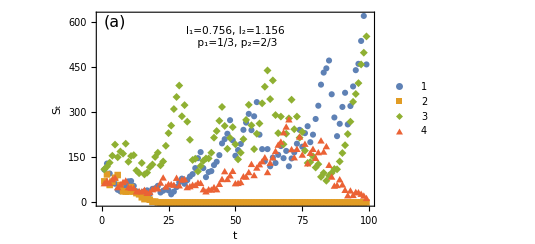

```mathematica
fig2a=ListPlot[{list,list2,list3,list4},
Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->10.5],FrameLabel->{Style["t",10.5,FontFamily->"Times New Roman"],Style["S_t",10.5,FontFamily->"Times New Roman"]},ImageSize->140*72/25.4,
PlotRange->{{0,100},Full},
PlotLegends->Placed[{1,2,3,4},{0.07,0.65}],PlotMarkers->Automatic,
Epilog->{Inset[Style["l_1=0.756, l_2=1.156\n p_1=1/3, p_2=2/3",FontFamily->"Times New Roman",FontSize->10.5],{50,550}],Text[StyleForm["(a)",FontSize->16],{5,600}]
}
]
```

```mathematica
ExtinctionProbability[time_]:=
Module[{Repetition=10000},Extinction=0;
Do[
Clear[size];size0=100;size[1]=size0;size[n_]:=size[n]=NextSize[size[n-1]];If[size[time]==0,Extinction++],Repetition
];1-N[Extinction/Repetition]]
```

```mathematica
listEP10000=Table[ExtinctionProbability[time],{time,1,100}]
```

```mathematica
listEP10000={1.,1.,1.,1.,1.,1.,1.,1.,1.,0.9998,1.,0.9999,0.9995,0.999,0.9989,0.9973,0.9971,0.9967,0.9945,0.995,0.9921,0.99,0.988,0.9874,0.9857,0.9836,0.9804,0.9748,0.9747,0.9696,0.9698,0.968,0.9642,0.9599,0.9515,0.9526,0.9493,0.9445,0.9379,0.9361,0.9319,0.9309000000000001,0.9237,0.9172,0.9113,0.9115,0.9067000000000001,0.8993,0.9025,0.8904,0.8936999999999999,0.8829,0.8755,0.882,0.8749,0.8703,0.866,0.8563000000000001,0.858,0.8551,0.8434,0.846,0.8374,0.8377,0.8367,0.8364,0.8363,0.8189,0.8107,0.8124,0.8065,0.8065,0.7997,0.8015,0.7979,0.7904,0.7947,0.7803,0.7761,0.7752,0.7741,0.7688,0.7645,0.7625,0.7569,0.7511,0.7505,0.7414000000000001,0.7455,0.7444999999999999,0.7422,0.7261,0.738,0.7258,0.7264999999999999,0.7248,0.7176,0.716,0.7092,0.7056}
```

```mathematica
listEP1000={1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999,0.999,1.,0.999,0.999,0.997,0.999,0.998,0.992,0.997,0.995,0.994,0.995,0.985,0.989,0.985,0.983,0.98,0.977,0.975,0.961,0.96,0.957,0.963,0.961,0.954,0.953,0.943,0.958,0.933,0.933,0.938,0.925,0.908,0.946,0.929,0.904,0.911,0.901,0.914,0.9,0.894,0.889,0.89,0.875,0.882,0.874,0.877,0.874,0.864,0.889,0.87,0.841,0.854,0.842,0.841,0.837,0.8200000000000001,0.83,0.823,0.792,0.8009999999999999,0.815,0.778,0.813,0.784,0.804,0.794,0.755,0.784,0.766,0.782,0.775,0.78,0.747,0.744,0.738,0.73,0.727,0.75,0.7150000000000001,0.758,0.738,0.752,0.747,0.739,0.751,0.7150000000000001,0.728,0.7110000000000001,0.721}
```

```mathematica
listEP100={1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.99,1.,0.99,0.99,0.99,0.98,0.99,0.99,0.99,0.95,0.99,0.97,0.99,0.98,0.97,0.9299999999999999,0.96,0.97,0.96,0.9299999999999999,0.91,0.91,0.94,0.89,0.92,0.9299999999999999,0.9,0.92,0.9,0.91,0.92,0.9,0.86,0.91,0.84,0.86,0.92,0.85,0.84,0.89,0.83,0.89,0.86,0.8200000000000001,0.86,0.84,0.83,0.87,0.77,0.89,0.81,0.8,0.83,0.83,0.76,0.78,0.81,0.75,0.84,0.78,0.85,0.76,0.74,0.71,0.8,0.71,0.76,0.75,0.77,0.77,0.76,0.74,0.74,0.71,0.69,0.6699999999999999,0.8,0.64,0.78,0.8,0.75,0.63}
```

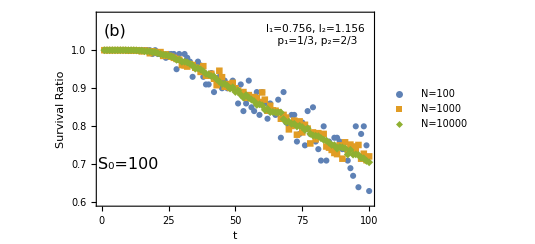

```mathematica
fig2b=ListPlot[{listEP100,listEP1000,listEP10000},
Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->10.5],FrameLabel->{Style["t",10.5,FontFamily->"Times New Roman"],Style["Survival Ratio",10.5,FontFamily->"Times New Roman"]},ImageSize->140*72/25.4,
PlotRange->{{0,100},{0.6,1.09}},
PlotLegends->Placed[{"N=100","N=1000","N=10000",4},{0.12,0.6}],PlotMarkers->Automatic,
Epilog->{Inset[Style["l_1=0.756, l_2=1.156\n p_1=1/3, p_2=2/3",FontFamily->"Times New Roman",FontSize->10.5],{80,1.04}],
Inset[Style["S_0=100",FontFamily->"Times New Roman",FontSize->16],{10,.7}],
Text[StyleForm["(b)",FontSize->16],{5,1.05}]
}
]
```

```mathematica
p1survival={{0.,0.6627000000000001},{0.05,0.5226},{0.1,0.3839},{0.15,0.2834},{0.2,0.19269999999999998},{0.25,0.121},{0.3,0.07579999999999998},{0.35,0.03590000000000004},{0.4,0.018399999999999972},{0.45,0.008399999999999963},{0.5,0.0030000000000000027}

}
```

```mathematica
p1survival2={{0.,0.8323},{0.05,0.6796},{0.1,0.5219},{0.15,0.3802},{0.2,0.256},{0.25,0.1673},{0.3,0.10299999999999998},{0.35,0.05120000000000002},{0.4,0.02300000000000002},{0.45,0.008399999999999963},{0.5169,0.0033999999999999586}}
```

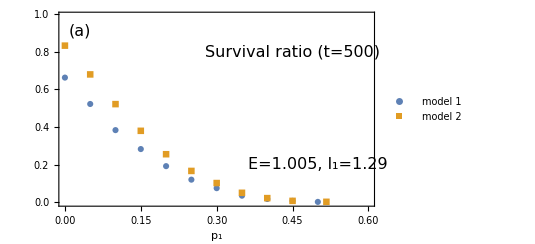

```mathematica
fig3a=ListPlot[{p1survival,p1survival2},


Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->10.5],FrameLabel->{Style["p_1",10.5,FontFamily->"Times New Roman"]},ImageSize->140*72/25.4,
PlotRange->{{0,0.6},{0,0.99}},
PlotMarkers->Automatic,



AxesLabel->{Style["p_1",FontSize->16,FontFamily->"Times New Roman"]},
PlotLegends->Placed[{Style["model 1",12,FontFamily->"Times New Roman"],
Style["model 2",12,FontFamily->"Times New Roman"]},{0.28,0.8}],
Epilog->{Text[Style["Survival ratio (t=500)",16,FontFamily->"Times New Roman"],{0.45,.8}],Text[Style["E=1.005, l_1=1.29",16,FontFamily->"Times New Roman"],{0.5,0.2}],Text[StyleForm["(a)",FontSize->16],{0.03,0.91}]
}]
```

```mathematica
l1survival={{0.9801986733067553,0.06577},{1,0.07194},{1.0253151205244289,0.07516},{1.0512710963760241,0.08431},{1.0778841508846315,0.0922},{1.1051709180756477,0.09916000000000003},{1.1331484530668263,0.10453999999999997},{1.161834242728283,0.11029},{1.191246216612358,0.11734999999999995},{1.2214027581601699,0.12024999999999997},{1.2523227161918644,0.12656999999999996},{1.2840254166877414,0.12988},{1.3165306748676215,0.13483},{1.3498588075760032,0.13932999999999995},{1.3840306459807514,0.14088},{1.4190675485932571,0.14471},{1.4549914146182013,0.14805999999999997},
{1.4918246976412703,0.15239999999999998}
}
```

```mathematica
l1survival2={{0.9595476587299596,0.09367999999999999},
{0.9801986733067553,0.1029},{1,0.11260999999999999},{1.0253151205244289,0.12446000000000002},{1.0512710963760241,0.13434999999999997},{1.0778841508846315,0.14290000000000003},{1.1051709180756477,0.15146000000000004},{1.1331484530668263,0.16080000000000005},{1.161834242728283,0.16990000000000005},{1.191246216612358,0.17581999999999998},{1.2214027581601699,0.18238},{1.2523227161918644,0.18832000000000004},{1.2840254166877414,0.19448},{1.3165306748676215,0.2005},{1.3498588075760032,0.20526999999999995},{1.4,0.20916999999999997}
}
```

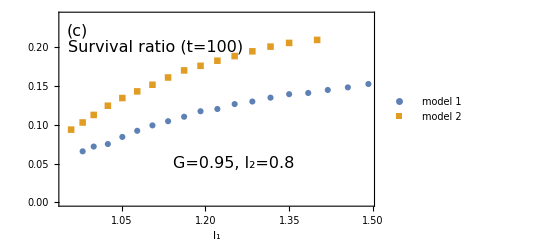

```mathematica
fig3c=ListPlot[{l1survival,l1survival2},AxesLabel->{Style["l_1",FontSize->16,FontFamily->"Times New Roman"]},
PlotLegends->Placed[{Style["model 1",12,FontFamily->"Times New Roman"],
Style["model 2",12,FontFamily->"Times New Roman"]},{0.9,0.2}],
Epilog->{Text[Style["Survival ratio (t=100)",16,FontFamily->"Times New Roman"],{1.11,0.2}],Text[Style["G=0.95, l_2=0.8",16,FontFamily->"Times New Roman"],{1.25,0.05}],Text[StyleForm["(c)",FontSize->16],{0.97,0.22}]}

,
Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->10.5],FrameLabel->{Style["l_1",10.5,FontFamily->"Times New Roman"]},ImageSize->140*72/25.4,
PlotMarkers->Automatic,PlotRange->{Automatic,{0,0.24}},


AxesLabel->{Style["p_1",FontSize->16,FontFamily->"Times New Roman"]},
PlotLegends->Placed[{Style["model 1",12,FontFamily->"Times New Roman"],
Style["model 2",12,FontFamily->"Times New Roman"]},{0.28,0.8}]

]
```

```mathematica
fsurvival100m2={{0.,0.621},{0.05,0.6844},{0.1,0.7388},{0.15,0.7914},{0.2,0.8204},{0.25,0.8397},{0.3,0.8555},{0.35,0.8737},{0.4,0.8775},{0.45,0.8838},{0.5,0.8846},{0.55,0.886},{0.6,0.8803},{0.65,0.8758},{0.7,0.8689},{0.75,0.8548},{0.8,0.8414},{0.85,0.8354},{0.9,0.8285},{0.95,0.8135},{1,0.7903}}
```

```mathematica
fsurvival200m2={{0.,0.11219999999999997},{0.05,0.15490000000000004},{0.1,0.22450000000000003},{0.15,0.30610000000000004},{0.2,0.38049999999999995},{0.25,0.4576},{0.3,0.5333},{0.35,0.5891},{0.4,0.6329},{0.45,0.669},{0.5,0.6823},{0.55,0.6965},{0.6,0.6990000000000001},{0.65,0.7081999999999999},{0.7,0.702},{0.75,0.7022999999999999},{0.8,0.6839999999999999},{0.85,0.6828000000000001},{0.9,0.6579999999999999},{0.95,0.6443},{1,0.6352}}
```

```mathematica
fsurvival300m2={{0.,0.013499999999999956},{0.05,0.031000000000000028},{0.1,0.05349999999999999},{0.15,0.09519999999999995},{0.2,0.14890000000000003},{0.25,0.23660000000000003},{0.3,0.3145},{0.35,0.3954},{0.4,0.45820000000000005},{0.45,0.5152},{0.5,0.5521},{0.55,0.5746},{0.6,0.5986},{0.65,0.6091},{0.7,0.6106},{0.75,0.6054999999999999},{0.8,0.5994999999999999},{0.85,0.5857},{0.9,0.5777},{0.95,0.5567},{1,0.5407}}
```

```mathematica
fsurvival400m2={{0.,0.0023999999999999577},{0.05,0.0050000000000000044},{0.1,0.012599999999999945},{0.15,0.02739999999999998},{0.2,0.0655},{0.25,0.11850000000000005},{0.3,0.1926},{0.35,0.272},{0.4,0.3498},{0.45,0.4173},{0.5,0.46730000000000005},{0.55,0.5107999999999999},{0.6,0.5287999999999999},{0.65,0.5385},{0.7,0.5617},{0.75,0.5598000000000001},{0.8,0.5492},{0.85,0.5327999999999999}}
```

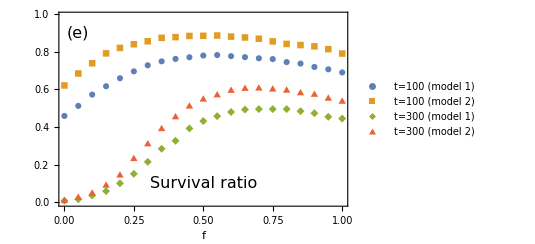

```mathematica
fig3e=ListPlot[{fsurvival100,fsurvival100m2,fsurvival300,fsurvival300m2}

,
PlotLegends->Placed[{Style["t=100 (model 1)",12,FontFamily->"Times New Roman"],
Style["t=100 (model 2)",12,FontFamily->"Times New Roman"],Style["t=300 (model 1)",12,FontFamily->"Times New Roman"],
Style["t=300 (model 2)",12,FontFamily->"Times New Roman"]

},{0.8,0.2}],

Epilog->{Text[Style["Survival ratio",16,FontFamily->"Times New Roman"],{.5,0.1}],Text[Style["G=0.95, l_2=0.8",16,FontFamily->"Times New Roman"],{1.25,0.05}],Text[StyleForm["(e)",FontSize->16],{0.05,0.9}]}

,
Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->10.5],FrameLabel->{Style["f",10.5,FontFamily->"Times New Roman"]},ImageSize->140*72/25.4,
PlotMarkers->Automatic,PlotRange->{Automatic,{0,0.99}}

]
```

```mathematica
listA={1.,1.,1.,1.,0.999955,0.999007,0.994246,0.981162,0.954976,0.913517,0.857208,0.789182,0.713479,0.6338820000000001,0.554093,0.477067,0.407216,0.34341,0.28720199999999996,0.23789300000000002,0.19572999999999996,0.16029300000000002,0.130069,0.10494899999999996,0.08456300000000005,0.06826699999999997,0.05494699999999997,0.04403800000000002,0.034984000000000015,0.02779799999999999,0.022101999999999955,0.01746000000000003,0.013905999999999974,0.011101999999999945,0.008850000000000025,0.006921999999999984,0.005481999999999987,0.0042959999999999665,0.003498000000000001,0.002677999999999958,0.0022100000000000453,0.0017089999999999606,0.0013739999999999863,0.0010289999999999466,0.0007819999999999494,0.0006150000000000322,0.0005049999999999777,0.00041000000000002146,0.0003260000000000485,0.00023899999999998922}
```

```mathematica
listB={1.,1.,1.,1.,0.999978,0.999455,0.996607,0.987583,0.968306,0.935888,0.889199,0.829321,0.7614,0.68686,0.611904,0.535826,0.46477100000000005,0.39741499999999996,0.336948,0.28387799999999996,0.23725300000000005,0.19703199999999998,0.16310899999999995,0.13462399999999997,0.10907900000000004,0.08935400000000004,0.07240199999999997,0.05891299999999999,0.04818500000000003,0.03831300000000004,0.03128299999999995,0.02534499999999995,0.020383999999999958,0.016043999999999947,0.01295500000000005,0.010311999999999988,0.008221999999999952,0.006610000000000005,0.005449999999999955,0.004342999999999986,0.0032889999999999864,0.0026359999999999717,0.002134999999999998,0.00172300000000003,0.001338999999999979,0.0010900000000000354,0.0008879999999999999,0.0006909999999999972,0.0005589999999999762,0.0004769999999999497}
```

```mathematica
listD={1.,1.,1.,1.,1.,0.999999,0.999969,0.999602,0.997502,0.990045,0.972544,0.938988,0.888131,0.820759,0.741449,0.65657,0.570183,0.486074,0.40956899999999996,0.341778,0.28239400000000003,0.23156200000000005,0.18779500000000005,0.152455,0.12184600000000001,0.09838800000000003,0.07916900000000004,0.06359800000000004,0.050651,0.040283999999999986,0.032206999999999986,0.025468000000000046,0.02046800000000004,0.016210999999999975,0.012954000000000021,0.010279999999999956,0.008325999999999945,0.006552000000000002,0.005225999999999953,0.0041759999999999575,0.0032640000000000446,0.0025049999999999795,0.0020529999999999715,0.0015840000000000298,0.0012790000000000301,0.0009869999999999601,0.0007949999999999902,0.0006599999999999939,0.0004809999999999537,0.0004030000000000422}
```

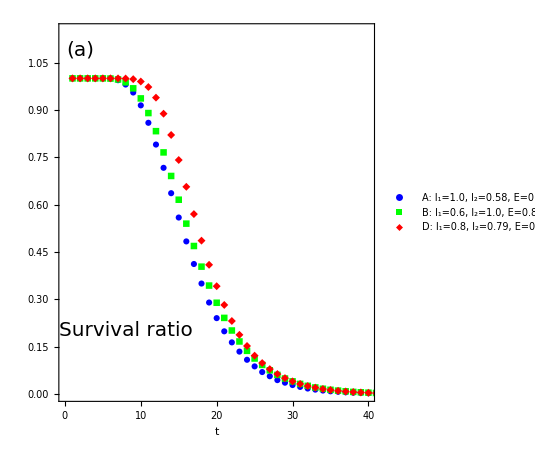

```mathematica
fig4a=ListPlot[{listA,listB,listD}
,
Axes->{True,False},AxesStyle->Directive[Black,AbsoluteThickness[0.5]],Frame->True,FrameStyle->AbsoluteThickness[0.5],FrameTicksStyle->Directive[AbsoluteThickness[0.5],FontFamily->"Times New Roman",FontSize->20],FrameLabel->{Style["t",20,FontFamily->"Times New Roman"]
(*,Style["Survival Ratio",10.5,FontFamily->"Times New Roman"]*)
},ImageSize->140*72/25.4,
PlotRange->{{0,40},{0,1.15}},AspectRatio->1.2,
PlotLegends->Placed[{Style["A: l_1=1.0, l_2=0.58,   \n    E=0.79, G=0.762",FontFamily->"Times New Roman",FontSize->15],Style["B: l_1=0.6, l_2=1.0,   \n    E=0.8, G=0.775",FontFamily->"Times New Roman",FontSize->15],Style["D: l_1=0.8, l_2=0.79,   \n    E=0.795, G=0.795",FontFamily->"Times New Roman",FontSize->15]},{.65,0.8}],
(*PlotLegends->Placed[{Style["A: l_1=1.0, l_2=0.58",FontFamily->"Times New Roman",FontSize->10.5],Style["B: l_1=0.6, l_2=1.0",FontFamily->"Times New Roman",FontSize->10.5],Style["D: l_1=0.8, l_2=0.79",FontFamily->"Times New Roman",FontSize->10.5]},{.7,0.8}],
*)
PlotMarkers->Automatic,PlotStyle->{Blue,Green,Red},
Epilog->{
(*Inset[Style["l_1=0.756, l_2=1.156\n p_1=1/3, p_2=2/3",FontFamily->"Times New Roman",FontSize->10.5],{80,1.04}],*)
(*Inset[inset,{32,.4}],*)Text[StyleForm["(a)",FontSize->20],{2,1.09}]
,Text[Style["Survival ratio",20,FontFamily->"Times New Roman"],{8,0.2}]
}
]
```